## Centroid-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.5 (6-Nov-2012)) loaded Fri 9 Nov 2012 04:17:19
using xCellerator 0.90 and XSSA 1204002

```mathematica
w=TemplateRandomSquareGrid[36, {-5,-5}, {5, 5}];
```

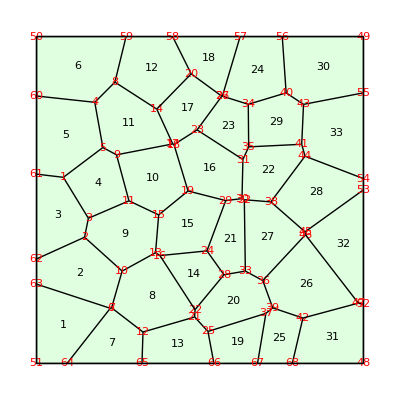

```mathematica
ShowTissue[w, "CellNumbers"-> True, "VertexNumbers"-> Red]
```

Determine the vertex numbers for cell 15

```mathematica
Centroid[w, 15]
```

{-0.358572,-0.748246}

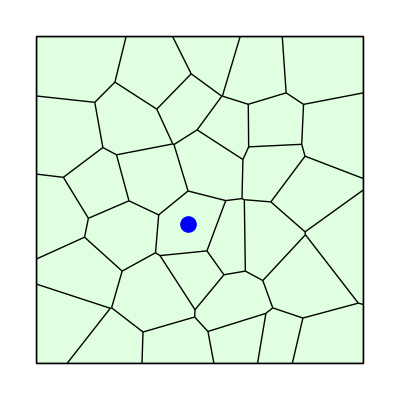

```mathematica
ShowTissue[w, Epilog-> {Blue, PointSize[.03], Point[Centroid[w,15]]}]
```

```mathematica
polygon = CellVertexCoordinates[w,15]
```

{{-1.36026,-1.61307},{-1.26373,-0.455218},{-0.365788,0.275456},{0.78698,-0.0182891},{0.212249,-1.55672},{-1.22428,-1.7005}}

```mathematica
c=Centroid[polygon]
```

{-0.358572,-0.748246}

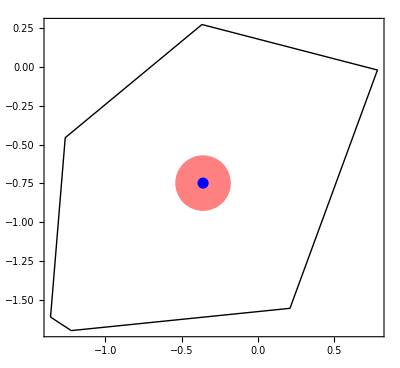

```mathematica
Show[Boundary[polygon], Graphics[{Pink, PointSize[.1], Point[c], Blue, PointSize[.02], Point[c]}], Frame-> True]
```